```mathematica
ClearAll["Global`*"]
Needs["ComputerArithmetic`"]

mypath = "~/Dropbox/Mathematica/Space/Exp/";
CreateDirectory[mypath] ;

Get["~/Dropbox/Mathematica/Space/MonitoredFindRoots.m"]
Get["~/Dropbox/Mathematica/Space/Param.m"]
Get["~/Dropbox/Mathematica/Space/PartialBalFunc.m"]
```

CreateDirectory::filex: /home/leon/Dropbox/Mathematica/Space/Exp/ already exists.

0.166293

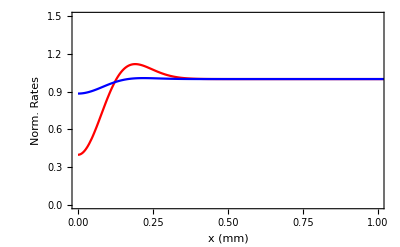

```mathematica
PARAM
σ0=0.1 ; Γ0=.1 ;
Γmax[σ0]
Plot[{Part[rPos[x,Γ0,σ0],1]/r0[[1]],Part[rPos[x,Γ0,σ0],2]/r0[[2]]},
	   {x, 0, L/2}, 
   	FrameLabel->{"x (mm)", "Norm. Rates"}, 
   	PlotRange->{{0,1},{0,1.5}}]
```

```mathematica
FindRoot[rPos[x,Γ0,σ0][[1]],{x,0,L/2}]
FindRoot[rPos[x,Γ0,σ0][[2]],{x,0,L/2}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→0.0900472}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→10.}

```mathematica
Get["~/Dropbox/Mathematica/Space/Inputs.m"]
PARAM
σ0=.1 ; Γ0=.5;
xcE[Γ0,σ0]
xcI[Γ0,σ0]
```

0.166175

0.166175

```mathematica
FindRoot[rNeg[x,xcI[Γ0,σ0],Γ0,σ0][[2]],{x,0,σ0}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→0.181391}

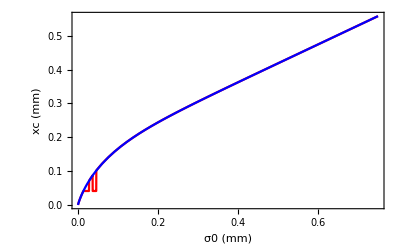

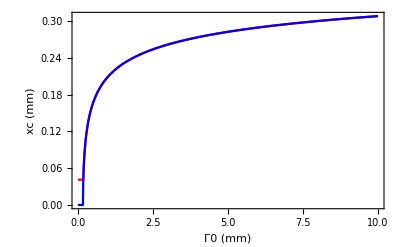

```mathematica
Plot[{xcE[Γ0,σ0],xcI[Γ0,σ0]},
	   {σ0, 0, L/4}, 
   	FrameLabel->{"σ0 (mm)", "xc (mm)"}]

σ0=.1 ; 
Plot[{xcE[Γ0,σ0],xcI[Γ0,σ0]},
	   {Γ0, 0, 10}, 
   	FrameLabel->{"Γ0 (mm)", "xc (mm)"}]
```

0.28593

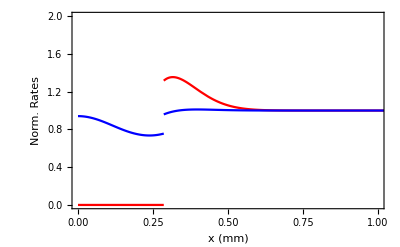

~/Dropbox/Mathematica/Space/Exp//left_profile_Cff_0.150G0_1.00.dat

~/Dropbox/Mathematica/Space/Exp//right_profile_Cff_0.150G0_1.00.dat

```mathematica
PARAM
Get["~/Dropbox/Mathematica/Space/Inputs.m"]
σ0=0.15 ; Γ0=Γmax[σ0]+.05 ;
Γ0=1 ;
XC = Chop[xcI[Γ0,σ0]]

pltPos = Plot[{Part[rPos[x,Γ0,σ0],1]/r0[[1]],Part[rPos[x,Γ0,σ0],2]/r0[[2]]}, {x, XC, L/2}] ;

If[XC>0,
	pltNeg = Plot[{rNeg[x,XC,Γ0,σ0][[1]]/r0[[1]],rNeg[x,XC,Γ0,σ0][[2]]/r0[[2]]}, {x, 0, XC}]; 
	Show[pltPos,pltNeg, FrameLabel->{"x (mm)", "Norm. Rates"}, PlotRange->{{0,1},{0,2}}],
	Show[pltPos, FrameLabel->{"x (mm)", "Norm. Rates"}, PlotRange->{{0,1},{0,2}}]
	]

left = Table[{x,rNeg[x,XC,Γ0,σ0][[1]]/r0[[1]],rNeg[x,XC,Γ0,σ0][[2]]/r0[[2]]},{x,0,XC,.01}]; 
leftfile = StringJoin[{mypath,"/left_profile_Cff_",ToString[NumberForm[σ0,{4,3}]],"G0_",ToString[NumberForm[Γ0,{4,2}]],".dat"}] 
Export[leftfile, left, "Table"] ;
right = Table[{x,rPos[x,Γ0,σ0][[1]]/r0[[1]],rPos[x,Γ0,σ0][[2]]/r0[[2]]},{x,XC,L/2,.01}] ;
rightfile = StringJoin[{mypath,"/right_profile_Cff_",ToString[NumberForm[σ0,{4,3}]],"G0_",ToString[NumberForm[Γ0,{4,2}]],".dat"}] 
Export[rightfile, right, "Table"] ;
```

```mathematica
rI[x_,Γ0_,σ0_] := rNeg[x,xcI[Γ0,σ0],Γ0,σ0][[2]] ;
minRi[Γ0_,σ0_] := First[FindMinimum[rI[x,Γ0,σ0] Γ0/(σ0+.001),{x,σ0},Method->"PrincipalAxis"]]
zeroRi[Γ0_,σ0_] := x/. First[monitoredFindRoot[rI[x,Γ0,σ0], {x, σ0, 2 σ0}, Method -> "Secant"] ] ;
```

```mathematica
minRi[1,0.01]
zeroRi[Γ0,σ0]
```

-219.226

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.287015

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

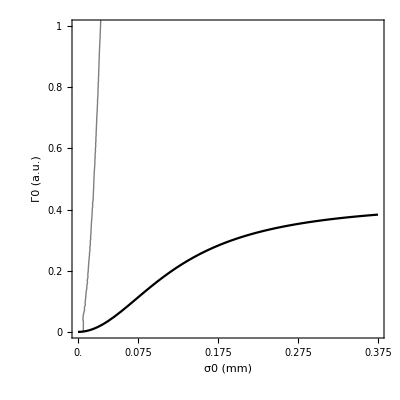

```mathematica
xcIplt = ContourPlot[minRi[Γ0,σ0],{σ0,0,.375},{Γ0,0,2},ColorFunction -> (If[#<0, Lighter[Blue, Abs[#]],
Lighter[White, #]] &), ColorFunctionScaling -> False, Contours->{0}] ;
xcEplt = Plot[Γmax[σ0], {σ0, 0, .375}, PlotStyle->Black, PlotRange->All, AxesOrigin -> {0, 0}] ;

Show[xcIplt,xcEplt,PlotRange->{{0,.375},{0,1}}, 
FrameTicks->{{0.,.075,.175,.275,.375},{0,.2,.4,.6,.8,1}}, FrameLabel -> {"σ0 (mm)", "Γ0 (a.u.)"}, Frame -> {{True, False}, {True, False}}]
```

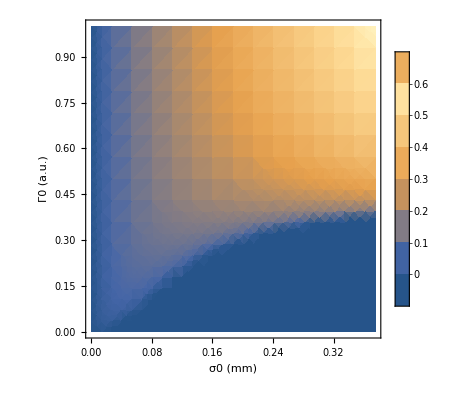

```mathematica
DensityPlot[xcI[Γ0,σ0],{σ0,0,.375},{Γ0,0,1},PlotLegends->{0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1}
,Frame -> {{True, False}, {True, False}}, FrameLabel -> {"σ0 (mm)", "Γ0 (a.u.)"}]
```

BarLegend::optx: Unknown option Label→{xc} in ….

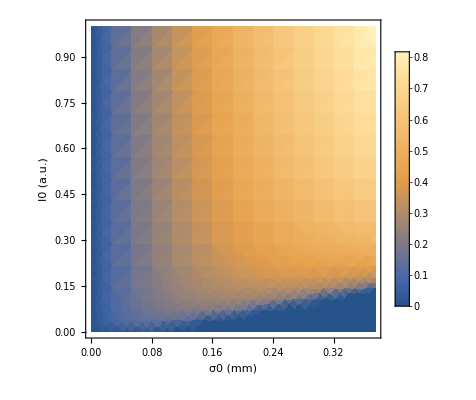

```mathematica
DensityPlot[xcI[Γ0/σ0,σ0],{σ0,0,.375},{Γ0,0,1},
PlotLegends->{Ticks->{0,.1,.2,.3,.4,.5,.6,0.7,0.8,0.9,1},TicksStyle->{FontSize->14}}
,Frame -> {{True, False}, {True, False}}, FrameLabel -> {"σ0 (mm)", "I0 (a.u.)"},BaseStyle->{FontSize->14}]
```

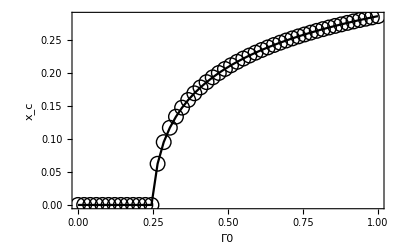

~/Dropbox/Mathematica/Space/Exp//xcVsG0_Cff_0.150.dat

```mathematica
PARAM
Get["~/Dropbox/Mathematica/Space/Inputs.m"]
Get["~/Dropbox/Mathematica/Space/xcVsG0.m"]

σ0 = .15 ;
Γ0List = Join[linearmesh[.0,1,50] //N] ;
xcVsΓ0

data = Transpose@{Γ0List,xcList};
xcPlt = ListLinePlot[data,FrameLabel->{"Γ0","x_c"},
					Frame->{{True,False},{True,False}},
					PlotRange->All,
					PlotMarkers->{○, 15}, 
					PlotStyle->Black]; 
Fig = Show[xcPlt]

datafile = StringJoin[{mypath,"/xcVsG0_","Cff_",ToString[NumberForm[σ0,{4,3}]],".dat"}] 
Export[datafile, data, "Table"] ;
```

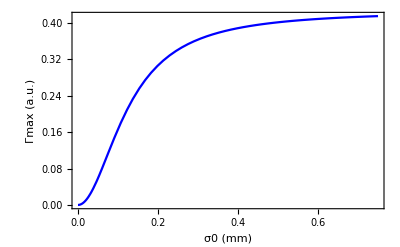

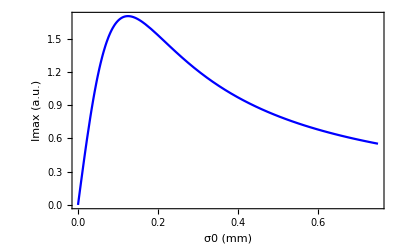

```mathematica
Plot[Γmax[σ0],{σ0, 0, L/4},FrameLabel->{"σ0 (mm)", "Γmax (a.u.)"}]
Plot[Γmax[σ0]/σ0,{σ0, 0, L/4},FrameLabel->{"σ0 (mm)", "Imax (a.u.)"}]
```

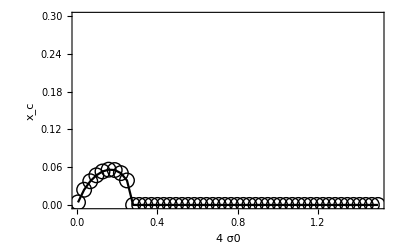

~/Dropbox/Mathematica/Space/Exp//xcVsCff_G0_0.10.dat

```mathematica
Get["~/Dropbox/Mathematica/Space/xcVsG0.m"]
Γ0 = .1; 

σ0List = linearmesh[.001,.375,50];
xcList = {} ;
xcVsσ0;

data = Transpose@{4 σ0List,xcList};
xcPlt = ListLinePlot[data,FrameLabel->{" 4 σ0","x_c"},
					Frame->{{True,False},{True,False}},
					PlotRange->All,
					PlotMarkers->{○, 15}, 
					PlotStyle->Black]; 
Fig = Show[xcPlt,PlotRange->{0,.3}]

datafile = StringJoin[{mypath,"/xcVsCff_","G0_",ToString[NumberForm[Γ0,{4,2}]],".dat"}] 
Export[datafile, data, "Table"] ;
```

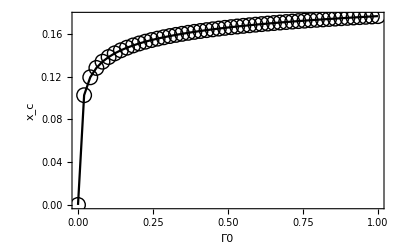

~/Dropbox/Mathematica/Space/Exp//xcVsG0_Cff_0.050_I0.dat

```mathematica
PARAM
Get["~/Dropbox/Mathematica/Space/Inputs.m"]
Get["~/Dropbox/Mathematica/Space/xcVsG0.m"]

σ0 = .05 ;
Γ0List = Join[linearmesh[.0,1,50] //N] ;
xcVsΓ0Int

data = Transpose@{Γ0List,xcList};
xcPlt = ListLinePlot[data,FrameLabel->{"Γ0","x_c"},
					Frame->{{True,False},{True,False}},
					PlotRange->All,
					PlotMarkers->{○, 15}, 
					PlotStyle->Black]; 
Fig = Show[xcPlt]

datafile = StringJoin[{mypath,"/xcVsG0_","Cff_",ToString[NumberForm[σ0,{4,3}]],"_I0.dat"}] 
Export[datafile, data, "Table"] ;
```

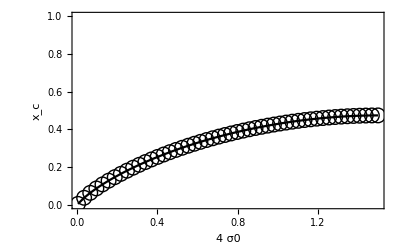

~/Dropbox/Mathematica/Space/Exp//xcVsCff_G0_0.25_I0.dat

```mathematica
Get["~/Dropbox/Mathematica/Space/xcVsG0.m"]
Γ0 = .25; 

σ0List = linearmesh[.001,.375,50];
xcList = {} ;
xcVsσ0Int;

data = Transpose@{4 σ0List,xcList};
xcPlt = ListLinePlot[data,FrameLabel->{" 4 σ0","x_c"},
					Frame->{{True,False},{True,False}},
					PlotRange->All,
					PlotMarkers->{○, 15}, 
					PlotStyle->Black]; 
Fig = Show[xcPlt,PlotRange->{0,1}]

datafile = StringJoin[{mypath,"/xcVsCff_","G0_",ToString[NumberForm[Γ0,{4,2}]],"_I0.dat"}] 
Export[datafile, data, "Table"] ;
```